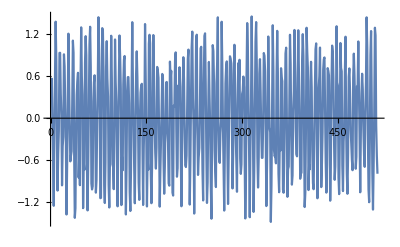

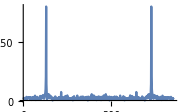
{0.04062,-Graphics-}

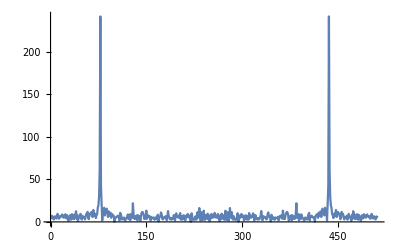
{0.08078,-Graphics-}

{0.11371,-Graphics-}

```mathematica
myfourier[x_]:=(
result={};
capn=Length[x];
Do[
nextX=Sum[x[[n+1]]*E^(-ⅈ*2*π*k*n/capn),{n,0,capn-1}];
result=Append[result,nextX];
,{k,0,capn-1}];
result
);
myfft[x_,capn_,s_]:=(
result={};
If[capn==1,
result=Append[result,x[[1]]],
result=Join[result,myfft[x,capn/2,2s]];
result=Join[result,myfft[x[[s+1;;]],capn/2,2s]];
Do[
t=result[[k+1]];
result[[k+1]]=t+E^(-ⅈ*2*π*k/capn)*result[[k+capn/2+1]];
result[[k+capn/2+1]]=t-E^(-ⅈ*2*π*k/capn)*result[[k+capn/2+1]];
,{k,0,capn/2-1}];
];
result
);
myfasterft[x_,capn_,s_,precomputed_]:=(
result={};
If[capn==1,
result=Append[result,x[[1]]],
result=Join[result,myfasterft[x,capn/2,2s,precomputed]];
result=Join[result,myfasterft[x[[s+1;;]],capn/2,2s,precomputed]];
Do[
t=result[[k+1]];
result[[k+1]]=t+precomputed[[Log2[capn]]][[k+1]]*result[[k+capn/2+1]];
result[[k+capn/2+1]]=t-precomputed[[Log2[capn]]][[k+1]]*result[[k+capn/2+1]];
,{k,0,capn/2-1}];
];
result
);
precomputedmatrix[datalen_]:=(
Table[
Table[
E^(-ⅈ*2*π*k/capn),
{k,0.,datalen/2-1}
],
{capn,Table[2^x,{x,1,Log2[datalen]}]}
]
)
data=Table[N[Sin[30 2 Pi n/200]+(RandomReal[]-1/2)],{n,512}];
ListLinePlot[data]
ListLinePlot[Abs[Fourier[data,FourierParameters->{1,-1}]],PlotRange->All]//AbsoluteTiming
precomputed=precomputedmatrix[Length[data]];
ListLinePlot[Abs[myfasterft[data,Length[data],1,precomputed]],PlotRange->All]//AbsoluteTiming
ListLinePlot[Abs[myfft[data,Length[data],1]],PlotRange->All]//AbsoluteTiming
(*ListLinePlot[Abs[myfourier[data]],PlotRange->All]//AbsoluteTiming*)
```

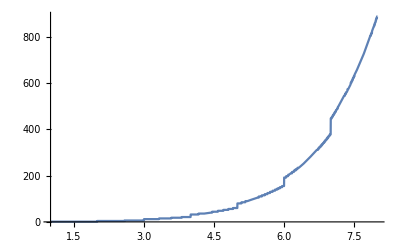

```mathematica
Plot[Times@@Dimensions[precomputedmatrix[2^n]],{n,1,8}]
```

```mathematica
Times@@Dimensions[precomputedmatrix[1024]]
```

5120